```mathematica
SetOptions[$FrontEnd,CommonDefaultFormatTypes->{"Output"->TraditionalForm}];
```

```mathematica
$LoadPhi=True;
```

```mathematica
Quiet[Needs["HighEnergyPhysics`fc`"]];
```

```mathematica
<<X`;
```

Package-X v1.0.4, by Hiren H. Patel

Package-X already initialized.

```mathematica
IntF/:MakeBoxes[IntF[exp_,___],TraditionalForm]:=RowBox[{"‖",MakeBoxes[exp,TraditionalForm],"‖"}];
```

```mathematica
SetOptions[Eps,Dimension->D];
SetOptions[LeviCivita,Dimension->D];
SetOptions[ScalarProduct,Dimension->D];
SetOptions[DiracMatrix,Dimension->D];
SetOptions[MetricTensor,Dimension->D];
SetOptions[SUNSimplify,SUNNToCACF->True];
SetOptions[SUNSimplify,Explicit->True];
SetOptions[SUNTrace,Explicit->False];
```

SetOptions::locked: Symbol TraditionalForm`DiracMatrix is locked.

```mathematica
ScalarProduct[qc,qc]=MC^2;
ScalarProduct[qb,qb]=MB^2;
```

```mathematica
ScalarProduct[p3,p3]=(MC+MB)^2;
ScalarProduct[p4,p4] =(MC+MB)^2;
```

```mathematica
ScalarProduct[p3,p4] =ms/2 -(MC+MC)^2;
```

$IterationLimit::itlim: Iteration limit of TraditionalForm`4096 exceeded.

```mathematica
ms=s (MC+MB)^2;
```

```mathematica
Momentum[qc,D]=r*Momentum[p3,D];
Momentum[qc]=r*Momentum[p3];
Momentum[qb,D]=(1-r)*Momentum[p4,D];
Momentum[qb]=(1-r)*Momentum[p4];
MC=r*m;
MB=(1-r)*m;
```

```mathematica
(*SpBcstar=1/(2 √2)(GS[p3]-MC-MB).GA[ψ1]//$ChangeDimension;*)
(*SpBc=1/(2 √2)(GS[p4]-MC-MB).GA[5]//$ChangeDimension;*)
```

```mathematica
PreFactor=(I π^(2-ϵ))/(Gamma[1-ϵ] (2 π)^(4-2 ϵ))  1/SUNN (Rs Rs)/(2 π (MC+MB));
```

```mathematica
Diagr=<<diagrBcnlo`;
AmpbeforeApart=<<AmpbeforeApartBcstarBcWest`;
AmpafterFire=<<AmpafterFireBcstarBcWest`;
AmpafterpackageX=<<AmpafterpackageXBcstarBc`;
```

```mathematica
DiagrPlot[n_]:=Module[{},
Print[Text[Style["Diagram  b,cbar->Bc*(p3, psi1)  bbar,c->Bc(p4):",FontSize->Large,FontColor->Blue]]];Paint[DiagramExtract[Diagr,n],ColumnsXRows->{2,2}];
Print[Text[Style["Amplitude before Apart (without PreFactor):",FontSize->Large,FontColor->Blue]]];
Print[AmpbeforeApart[[n]]];
Print[Text[Style["Amplitude after Fire (without PreFactor):",FontSize->Large,FontColor->Blue]]];
Print[AmpafterFire[[n]]];
Print[Text[Style["Amplitude after packageX (without PreFactor):",FontSize->Large,FontColor->Blue]]];
Print[AmpafterpackageX[[n]]];
(*Print[Text[Style["Final amplitude:",FontSize->Large,FontColor->Blue]]];
Print[Ampfinal[[n]]];
Print[Text[Style["Infinite terms of amplitude:",FontSize->Large,FontColor->Blue]]];
Print[Series[Ampfinal[[n]]+1/ϵ^3,{ϵ,0,-1}]-1/ϵ^3];
Print[Text[Style["Amplitude at large s:",FontSize->Large,FontColor->Blue]]];
Print[Series[Ampfinal[[n]],{s,Infinity,4}]];*)
Return[];
];
```

```mathematica
(* Amp 17,18,19,20,21,22,23,24,25,26,27,28 == 0   *)
```

Diagram  b,cbar->Bc*(p3, psi1)  bbar,c->Bc(p4):

> Top. 1: 1 diagram

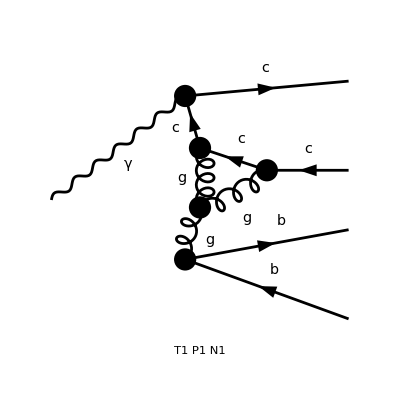

Amplitude before Apart (without PreFactor):

(ⅈ e C_A (1-C_A^2) g_s^4 ϵ^(γψ1 p_3 p_4) (-3 D m^2 r s k_1·p_3+3 D m^2 r s k_1·p_4+3 D m^2 s k_1·p_3-3 D m^2 s k_1·p_4-4 D (k_1·p_4)^2+4 D k_1·p_3 k_1·p_4+16 m^2 r s k_1·p_3-22 m^2 r s k_1·p_4+12 m^2 r k_1·p_3+12 m^2 r k_1·p_4-16 m^2 s k_1·p_3+18 m^2 s k_1·p_4-4 m^2 k_1·p_3-4 m^2 k_1·p_4+2 m^2 s k_1^2-8 m^2 k_1^2+8 (k_1·p_4)^2-8 k_1·p_3 k_1·p_4+m^4 r^2 s^2-4 m^4 r^2 s-m^4 r s^2+4 m^4 r s))/(6 m^5 (r-1)^3 (s-4) s^2 k_1^2 (2 r k_1·p_4-k_1^2) (-2 r k_1·p_3-2 r k_1·p_4+2 k_1·p_3+2 k_1·p_4+k_1^2+m^2 r^2 s-2 m^2 r s+m^2 s))

Amplitude after Fire (without PreFactor):

(ⅈ C_A (1-C_A^2) e (3 r D-3 D-19 r+17) ϵ^(γψ1 p_3 p_4) ‖1/(k_1^2 (r^2 s m^2-2 r s m^2+s m^2+k_1^2-2 r k_1·p_3+2 k_1·p_3-2 r k_1·p_4+2 k_1·p_4))‖ g_s^4)/(6 m^3 (1-r)^3 r (4-s) s)-(ⅈ C_A (1-C_A^2) e (3 D s r-18 s r-4 r-3 D s+16 s+4) ϵ^(γψ1 p_3 p_4) ‖1/(k_1^2 (k_1^2-2 r k_1·p_3) (r^2 s m^2-2 r s m^2+s m^2+k_1^2-2 r k_1·p_3+2 k_1·p_3-2 r k_1·p_4+2 k_1·p_4))‖ g_s^4)/(12 m (1-r)^2 (4-s) s)+((ⅈ C_A (1-C_A^2) (2-D) e (s r-2 r-s) ϵ^(γψ1 p_3 p_4) g_s^4)/(12 m^5 (1-r)^3 r (4-s) s^2 (r^2-s r+s))+(ⅈ C_A (1-C_A^2) (D-2) e (3 D s r-16 s r-12 r-3 D s+16 s+4) ϵ^(γψ1 p_3 p_4) g_s^4)/(24 (D-3) m^5 (1-r)^4 r^2 (4-s) s^2)-(ⅈ C_A (1-C_A^2) (2-D) e (2 r-s) ϵ^(γψ1 p_3 p_4) g_s^4)/(12 m^5 (1-r)^3 r (4-s) s^2 (r^2-s r+s))) ‖1/(k_1^2-2 r k_1·p_3)‖+((ⅈ C_A (1-C_A^2) e (3 D s r^2-18 s r^2-4 r^2-9 D s r+52 s r+12 r+6 D s-34 s) ϵ^(γψ1 p_3 p_4) g_s^4)/(12 m^3 (1-r)^4 r (4-s) s^2)+(ⅈ C_A (1-C_A^2) (2-D) e (r-1) (2 r^2-2 s r+2 r+s) ϵ^(γψ1 p_3 p_4) g_s^4)/(12 m^3 (1-r)^3 r (4-s) s (r^2-s r+s))-(ⅈ C_A (1-C_A^2) (2-D) e (r-1)^2 (2 r-s) ϵ^(γψ1 p_3 p_4) g_s^4)/(12 m^3 (1-r)^3 r (4-s) s (r^2-s r+s))) ‖1/((k_1^2-2 r k_1·p_3) (r^2 s m^2-2 r s m^2+s m^2+k_1^2-2 r k_1·p_3+2 k_1·p_3-2 r k_1·p_4+2 k_1·p_4))‖

Amplitude after packageX (without PreFactor):

1/(12 m^5 (r-1)^4 (s-4) s^2)ⅈ e C_A^2 C_F g_s^4 ϵ^(γψ1 p_3 p_4) (1/(r (r^2-r s+s))2 m^2 (r^4 (3 (D-6) s-4)+r^3 (-4 (D-5) s^2+(48-5 D) s+12)+2 r^2 s (D (7 s-1)-37 s-17)+4 r s (-4 D s+D+22 s+1)+2 (3 D-17) s^2) B_0(m^2 (r^2-r s+s);m r,0)-(4 m^2 (r-1) s (3 D (r-1)-19 r+17) B_0(m^2 (r-1)^2 s;0,0))/r-2 m^4 (r-1)^2 s (r (3 (D-6) s-4)+(16-3 D) s+4) C_0(m^2 r^2,m^2 (r-1)^2 s,m^2 (r^2-r s+s);0,m r,0)+((D-2) (r^3 (D (5 s-8)-22 s+12)+r^2 (D (-3 s^2-5 s+8)+16 s^2+34 s-20)+2 r s ((3 D-16) s-8)+s ((16-3 D) s+4)) A_0(m r))/((D-3) r^2 (r^2-r s+s)))

```mathematica
DiagrPlot[2];
```

```mathematica
Amp[1]
```

$Failed[1]